```mathematica
(** This is code modified specifically for the 2d case **)
(** Set the directory that you want your plots to go to here **)
SetDirectory["/users/maxzweig/fuelthrust"];
Off[General::stop];

Off[Solve::svars];
Off[FindRoot::lstol];
Off[InterpolatingFunction::dmval];
(** gets the axes for the energy limited reachable set associated with a given terminal time and thrust **)

xrf[tf_, delta_, h_, deltaT_, n_, Rr_, emax_] := 
NIntegrate[  emax ({{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}} // Transpose).{{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}}.delta / (deltaT.({{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}} // Transpose).{{-Sin[n (tau-tf)]/n,(2 (-1+Cos[n (tau-tf)]))/n,0},{-(2 (-1+Cos[n (tau-tf)]))/n,3 tau-3 tf-(4 Sin[n (tau-tf)])/n,0},{0,0,-Sin[n (tau-tf)]/n}}.delta // Sqrt)[[1]]  ,{tau, 0, tf}];

(** Computes the thrust-limited reachable set for a given final time **)
thrustreachable[xrf_,tf_, na_, emax_,numpoints_] := Module[{points, tfs, hs, As, ns, Rrs, pointsT, rd, rdpoints, rdboundary, first2},
points = CirclePoints[numpoints];
points = Append[#, 0] & /@ points;
points //  N;
points[[1]];
tfs = ConstantArray[tf, numpoints];
tfs[[1]];
hs = ConstantArray[1, numpoints];
hs[[1]];
ns = ConstantArray[na, numpoints];
ns[[1]];
Rrs = ConstantArray[1, numpoints];
Rrs[[1]];
emaxs = ConstantArray[emax, numpoints];
columntorow[x_] := {x};
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;

rd = MapThread[xrf, {tfs, points, hs, pointsT, ns, Rrs, emaxs}];
rdpoints = Map[Re, rd, {2}];
(* first2[x_] := {x[[1]], x[[2]]}; *)
(* rboundary = Map[first2, rdboundary];*)
rdpoints
]

getAxes[terminaltime_, quadform_, thrustmax_] := Module[{testbounds, teststats},
energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
vecs = energysetaxes[quadform];
vals = energyseteigenvalues[quadform];
ax1 = vecs[[1]][[1;;2]] * ((terminaltime thrustmax^2* vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((terminaltime thrustmax^2* vals[[2]]) // Sqrt);
{ax1,ax2}]

(** gets the minimum and maximum ratios between an energy limited set and an arbitrary reachable set given as set of points **)
reachablestatsoperator[points_,axis1_,axis2_] := Module[{rats, vecs}, 
ellipseVecFromUnitVec[uv_,ax1_, ax2_]:=1/Sqrt[(Normalize[ax1].uv)^2/Norm[ax1]^2+(Normalize[ax2].uv)^2/Norm[ax2]^2]*uv;
ratio[pos_]:= Norm[ellipseVecFromUnitVec[Normalize[pos[[1;;2]]],axis1, axis2] ]/ Norm[pos[[1;;2]]];
maxminrat[ v1s_] := {(ratio/@v1s)// Max, (ratio/@v1s)// Min};
toq2q1[vec_] := If[(vec[[1]] < 0 && vec[[2]] < 0) || (vec[[1]] >0 && vec[[2]] < 0), -vec, vec];
maxminvec[ v1s_] := {v1s[[ Position[(ratio/@v1s), (ratio/@v1s) // Max    ][[1,1]]]] // toq2q1 , v1s[[ Position[(ratio/@v1s), (ratio/@v1s) // Min   ][[1,1]]]] // toq2q1};
rats = maxminrat[ points];
vecs = maxminvec[ points];
{rats , {vecs[[1, 1;;2]], vecs[[2, 1;;2]]}}
] ;

(* computes minimum and maximum ratios between the thrust limited and thrust/fuel limited reachable sets, given as a set of points that are indexed by angle in their arrays.
Precondition is that no zeros or contained. *)
thrustfuelstats[thrustpoints_, fuelpoints_] := Module[{rats, vecs},

ListRatios[list1_, list2_] := MapThread[#1/#2&,{list1,list2}];
ratios = ListRatios[Map[Norm, thrustpoints], Map[Norm, fuelpoints]];
maxratio = ratios // Max;
minratio = ratios // Min;

toq2q1[vec_] := If[(vec[[1]] < 0 && vec[[2]] < 0) || (vec[[1]] >0 && vec[[2]] < 0), -vec, vec];

maxpos = Position[ratios, maxratio][[1,1]];
minpos = Position[ratios, minratio][[1,1]];

(**
maxpos = {fuelpoints[[maxpos]] // toq2q1, thrustpoints[[maxpos]] // toq2q1};
minpos = {fuelpoints[[minpos]] // toq2q1, thrustpoints[[minpos]] // toq2q1};
**)

maxpos = fuelpoints[[maxpos]] // toq2q1;
minpos = fuelpoints[[minpos]] // toq2q1;

{maxratio, minratio, maxpos, minpos}
];
getFinalEnergyPos[tt_, tmax_, nt_, delta_] := Module[{},
energyform[tff_, na_] := Module[{c, r, sig, gamma, nmat},
c[n_] = {
{0, -2* n, 0, 1, 0, 0},
{2 * n, 0, 0, 0, 1, 0},
{0, 0, 0, 0,0 , 1},
{-1, 0, 0, 0, 0, 0},
{0, -1, 0, 0,0,0 }, 
{0, 0, -1, 0, 0, 0 }
}; (*Good*)
c[n] // MatrixForm;
r[t_, h_] = {{72 t Cos[h t]+(154 h t+48 h^3 t^3-384 Sin[h t]-27 Sin[2 h t])/(4 h),-3 h t^2+(6-6 Cos[h t])/h,0,(8+12 h^2 t^2-8 Cos[h t]-24 h t Sin[h t]+9 Sin[h t]^2)/(2 h^2),(23 h t+6 h^3 t^3+42 h t Cos[h t]-56 Sin[h t]-9/2 Sin[2 h t])/h^2,0},{-3 h t^2+(6-6 Cos[h t])/h,t,0,(2 (-h t+Sin[h t]))/h^2,-(3 t^2)/2+(4-4 Cos[h t])/h^2,0},{0,0,(2 h t+Sin[2 h t])/(4 h),0,0,Sin[h t]^2/(2 h^2)},{(8+12 h^2 t^2-8 Cos[h t]-24 h t Sin[h t]+9 Sin[h t]^2)/(2 h^2),(2 (-h t+Sin[h t]))/h^2,0,(26 h t-32 Sin[h t]+3 Sin[2 h t])/(4 h^3),(3 (-h t+Sin[h t])^2)/h^3,0},{(23 h t+6 h^3 t^3+42 h t Cos[h t]-56 Sin[h t]-9/2 Sin[2 h t])/h^2,-(3 t^2)/2+(4-4 Cos[h t])/h^2,0,(3 (-h t+Sin[h t])^2)/h^3,(14 h t+3 h^3 t^3+24 h t Cos[h t]-32 Sin[h t]-3 Sin[2 h t])/h^3,0},{0,0,Sin[h t]^2/(2 h^2),0,0,-(-2 h t+Sin[2 h t])/(4 h^3)}};(*Good*)
r[t, n] // MatrixForm;
sig[t_, n_] = {{4-3 Cos[n t],0,0,Sin[n t]/n,(2-2 Cos[n t])/n,0},{6 (-n t+Sin[n t]),1,0,(2 (-1+Cos[n t]))/n,-3 t+(4 Sin[n t])/n,0},{0,0,Cos[n t],0,0,Sin[n t]/n},{3 n Sin[n t],0,0,Cos[n t],2 Sin[n t],0},{6 n (-1+Cos[n t]),0,0,-2 Sin[n t],-3+4 Cos[n t],0},{0,0,-n Sin[n t],0,0,Cos[n t]}}; (* Good *)
gamma[t_, t0_, n_] = sig[t, n]. (sig[t0, n] // Inverse);
nmat[t0_, tf_, n_] = (Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2] // Transpose). (c[n] // Transpose). (r[tf, n] // Inverse).c[n].Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2];
nmat[0, tff, na]
];

udd = IdentityMatrix[6] - Outer[Times, Join[{delta[[2]], -delta[[1]]}, {0,0,0,0}], Join[{delta[[2]], -delta[[1]]}, {0,0,0,0}]];
basis = Orthogonalize[udd];
projmat = Join[{basis[[1]]}, basis[[3;;]]] // Transpose;
projmatT = projmat // Transpose;
selectionMat = {{1,0,0,0,0,0}, {0,1,0,0,0,0}, {0,0,0,0,0,0}, {0,0,0,0,0,0}, {0,0,0,0,0,0}, {0,0,0,0,0,0}};
eformxf = energyform[tt, nt][[7;;12, 7;;12]];
ydir = Eigenvectors[{projmatT.selectionMat.projmat, projmatT.eformxf.projmat}][[1]];

xdir = projmat.ydir;
tmag = (tt tmax^2 / (xdir.eformxf.xdir)) // Sqrt;
xdir = If[xdir[[1]] delta[[1]] < 0, -xdir, xdir];

Print["energy computation executed"];
xdir tmag
];
propStateCostatev2[ics_, isp_, tf_] := Module[{vars, dyn},
mag[lxv_, lyv_, lzv_] :=(lxv ^ 2+ lyv ^2 + lzv ^2) // Sqrt;
switchingfunc [lxv_, lyv_, lzv_, lmag_, mas_, c_] := mag[lxv, lyv, lzv] - lmag mas /c; 
vars={x,y,z,vx,vy,vz,m,lxr,lyr,lzr,lxv,lyv,lzv,lm};
eqnsOpt = Join[(- A // Transpose).{lxr, lyr, lzr, lxv, lyv, lzv}, {( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2)tmax mag[lxv, lyv, lzv]  / (m ^2)}];
eqnsStateOpt={  2 vy n + 3n^2 x,    -2 n vx, - n^2 z  } + (1/m)( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2) tmax {lxv, lyv, lzv} / mag[lxv, lyv, lzv];
dyn=Join[Join[{vx,vy,vz},Join[eqnsStateOpt, {- ( 1/2 +Sign[switchingfunc[lxv, lyv, lzv , lm, m, isp]] / 2)tmax/isp}]],eqnsOpt];

soln =  NDSolveValue[
Join[Thread[(#'[t]&/@vars[[1;;14]])==(dyn/.Thread[vars->(#[t]&/@vars)])],
Thread[(#[0]&/@vars)==ics]],
vars,  {t, tf, tf}
];
#[tf]&/@soln
]
findInitialCostates[icRel_, fcRel_, n_, A_, td_, mmax_, m0_, tmax_] := Module[{vars, dyn},
eqnsStateOpt={  2 vy n + 3n^2 x,    -2 n vx, - n^2 z  } - {lxv, lyv, lzv};
eqnsOpt = (- A // Transpose).{lxr, lyr, lzr, lxv, lyv, lzv};
getInitCostates[varMat_,icsRel_,fcsRel_]:=LinearSolve[varMat[[1;;6,7;;12]],fcsRel-varMat[[1;;6,1;;6]].icsRel];
topLeftMatrix=A;
topRightMatrix=ConstantArray[0,{3,6}];
middleLeftMatrix=ConstantArray[0,{3,3}];
middleRightMatrix=-IdentityMatrix[3];
     bottomRightMatrix=-A // Transpose;
bottomLeftMatrix=ConstantArray[0,{6,6}];
fullmatrix = Join[Join[A, Join[ topRightMatrix, Join[middleLeftMatrix, middleRightMatrix, 2]], 2], Join[bottomLeftMatrix, bottomRightMatrix, 2 ] ];
stm[tf_] := MatrixExp[fullmatrix tf];
initCo = getInitCostates[stm[td], icRel, fcRel];
lambdastm[ta_] = MatrixExp[(-A // Transpose) ta];
lma = isp ((lambdastm[mmax isp / tmax].initCo)[[4;;6]]   // Norm)/(m0 - mmax) - NIntegrate[  tmax(((lambdastm[t].initCo)[[4;;6]]) // Norm) / ((m0 - tmax t / isp) ^2), {t, 0, mmax isp / tmax}];
initCoM = Join[initCo, {lma}];
initCoM
]
rootfind[init_, mm_, direction_, A_, m0_, isp_, timeLength_] := Module[{},
s = MatrixExp[-(A //Transpose) timeLength];
ly = init[[2]];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
falt[joint_]:= Module[{out},
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{joint[[1]] , ly, 0}, ({v4, v5} /. subs ) /. {v1->joint[[1]], v2 ->ly} ], {0, joint[[2]]}]], isp, timeLength];
cons[dey_, lf_, xf_, mmax_] := Module[{},
udd = (2 // IdentityMatrix) - ({dey} // Transpose).{dey};
c1 ={ (udd.{xf[[1]], xf[[2]]})[[1]] } ;
c2 =  If [timeLength tmax / isp<=mmax, {(m0 - xf[[7]]) -timeLength tmax / isp}, {(m0 - xf[[7]]) -mmax}];
Join[c1, c2] // Flatten
];
cons[direction, out[[8;;14]], out[[1;;7]] , mm]
];
poss = Catch[FindRoot[falt[l], {{l, {init[[1]], init[[3]]} }}, Evaluated->False, PrecisionGoal->20]];

(** if poss does not satisfy the directional and mass constraints within satisfaction, try again with the two other possible values for lambda y, and pick the best **)
{poss[[1, 2, 1]], ly, poss[[1, 2, 2]]}
]
rootfindalt2[init_, mm_, direction_, A_, m0_, isp_, timeLength_] := Module[{},
s = MatrixExp[-(A //Transpose) timeLength];
lx = init[[1]];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
falt[joint_]:= Module[{out},
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{lx , joint[[1]], 0}, ({v4, v5} /. subs ) /. {v1->lx, v2 ->joint[[1]]} ], {0, joint[[2]]}]], isp, timeLength];
cons[dey_, lf_, xf_, mmax_] := Module[{},
udd = (2 // IdentityMatrix) - ({dey} // Transpose).{dey};
c1 ={ (udd.{xf[[1]], xf[[2]]})[[1]] } ;
c2 =  If [timeLength tmax / isp<=mmax, {(m0 - xf[[7]]) -timeLength tmax / isp}, {(m0 - xf[[7]]) -mmax}];
Join[c1, c2] // Flatten
];
cons[direction, out[[8;;14]], out[[1;;7]] , mm]
];
poss = FindRoot[falt[l], {{l, {init[[2]], init[[3]]} }}, Evaluated->False, PrecisionGoal->20];

(** if poss does not satisfy the directional and mass constraints within satisfaction, try again with the two other possible values for lambda y, and pick the best **)
{lx, poss[[1, 2, 1]], poss[[1, 2, 2]]}
]

getReachablePoint[direction_, endTime_, tmax_, n_, m0_, A_, fuelpercent_, isp_] := Module[{},
posf = getFinalEnergyPos[endTime, tmax, n, direction];
s = MatrixExp[-(A //Transpose) endTime];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
initCostates = findInitialCostates[{0,0,0,0,0,0}, posf, n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ];
initialGuess2 = Join[{initCostates[[1]], initCostates[[2]]},{initCostates[[7]]}];
lxm2 = rootfind[initialGuess2,  tmax fuelpercent endTime / isp, direction // N, A, m0, isp, endTime];
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{lxm2[[1]], lxm2[[2]], 0}, ({v4, v5} /. subs ) /. {v1->lxm2[[1]], v2 ->lxm2[[2]]}, {0, lxm2[[3]]}]]], isp, endTime];
Print[out[[1;;2]]];
out[[1;;2]]
]

solveBVPsNested[initialAngle_, initialGuess_, endTime_, tmax_, n_, m0_, A_, fuelpercent_, isp_, numPoints_] := Module[{},
(** returns the direction the initial costate was computed in, as well as the initial costate 
	initialGuess contains all of the costates. 
  If prevDirectionCostate costate is identically 0, do the energy computation to obtain an initial guess. 
  Homotopy from delta to delta to travese the ring. If / when constraint isn't satisfied, perform the energy computation to obtain a new initial guess and try again.
**)
bvpNester[prevAngleCostatePosition_] := Module[{},
prevAngle = prevAngleCostatePosition[[1]];
prevCostate = prevAngleCostatePosition[[2]];
prevPosition = prevAngleCostatePosition[[3]];

nextAngle = prevAngle + 2 * Pi / numPoints;
nextDirection = {Cos[nextAngle], Sin[nextAngle]} // N;

nextCostate = If[prevCostate == {0,0,0}, findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmax, n, nextDirection], n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ][[{1, 2, 7}]], prevCostate];

nextGuess = {nextCostate[[1]],nextCostate[[2]], nextCostate[[3]]};
lxm2 = rootfind[nextGuess,  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime];
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{lxm2[[1]], lxm2[[2]], 0}, ({v4, v5} /. subs ) /. {v1->lxm2[[1]], v2 ->lxm2[[2]]}, {0, lxm2[[3]]}]]], isp, endTime];

terminalAngle = If[out[[1]] == 0 && out[[2]] == 0, 10000, ArcTan[out[[1]], out[[2]]]];
terminalMass = m0 - out[[7]];

(** retrying with energy optimal initial guess if necessary**)
 nextGuessReturn = If[Abs[(terminalAngle + Pi) - Mod[nextAngle, 2 Pi]] < 0.0025 && Abs[terminalMass / (tmax fuelpercent endTime / isp) - 1] < 0.01,{lxm2[[1]], lxm2[[2]], lxm2[[3]]}, 
rootfind[findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmax, n, nextDirection], n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ][[{1, 2, 7}]],  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime ]
];

out2 = propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{nextGuessReturn[[1]], nextGuessReturn[[2]], 0}, ({v4, v5} /. subs ) /. {v1->nextGuessReturn[[1]], v2 ->nextGuessReturn[[2]]}, {0, nextGuessReturn[[3]]}]]], isp, endTime];

(** if still failure to perfectly satisfy constraints, retrying with alternate optimization holding x constant and allowing changes in y **)
terminalAngle = If[out2[[1]] == 0 && out2[[2]] == 0, 10000, ArcTan[out2[[1]], out2[[2]]]];
If[ (out2[[1]] == 0  && out2[[2]] ==0)  || Abs[terminalMass / (tmax fuelpercent endTime / isp) - 1] >= 0.001 || Abs[(terminalAngle + Pi) - Mod[nextAngle, 2 Pi]] >= 0.0025,
( res = rootfindalt2[{nextGuessReturn[[1]], nextGuessReturn[[2]], nextGuessReturn[[3]]},  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime];
out3 = propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{res[[1]], res[[2]], 0}, ({v4, v5} /. subs ) /. {v1->res[[1]], v2 ->res[[2]]}, {0, res[[3]]}]]], isp, endTime];
Print[res];
Print[({v4, v5} /. subs) /. {v1 -> res[[1]], v2 -> res[[2]]}];
Print[nextDirection ];
{nextAngle, res, out3[[1;;2]], out3[[7]]}
),{nextAngle, nextGuessReturn, out2[[1;;2]], out2[[7]]}
]
];
NestList[bvpNester, {initialAngle, initialGuess, {0,0,0,0,0,0,0}}, numPoints]
]
```

```mathematica
mu1 = 3.986 10^14 ;
endTime = 3600;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
isp = 10000;
tmax = 0.002;
mmax = 0.002 endTime / isp;
m0 = 1;
```

```mathematica
computestats[thrustmax_, n_, endTime_, m0_, fuelpercent_, isp_, num_] := Module[{testbounds, teststats},
Print[fuelpercent];
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
testbounds = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num][[2;;]];
testbounds2 = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, 1, isp, num][[2;;]];

testmasses = testbounds[[;;,4]];
testmasses2= testbounds2[[;;, 4]];
testxfs = testbounds[[;;, 3]];
testxfs2 = testbounds2[[;;, 3]];

removalIndices = Position[Map[Norm, testxfs],_?((#!=0)&)] // Flatten;
augRemIndices = Position[Map[Norm, testxfs2],_?((#!=0)&)] // Flatten;
massRemIndices = Position[testmasses, _? (( Abs[#/ ((thrustmax fuelpercent endTime / isp) - m0)] - 1 <= 0.001) &)] // Flatten;
augMessRemIndices = Position[testmasses2, _? (( Abs[#/ ((thrustmax endTime / isp) - m0)] - 1<= 0.001) &)] // Flatten;

rats = MapThread[Abs[ArcTan[#1[[1]], #1[[2]]] - ArcTan[#2[[1]],#2[[2]]]] &, {testxfs, testxfs2}];
addRem = Position[rats, _? (( Abs[#] < 0.01) &)] //Flatten;

remInds = Intersection[augRemIndices, removalIndices, massRemIndices, augMessRemIndices, addRem];

thrustfuelstats[testxfs[[remInds]], testxfs2[[remInds]]]
]


(** plots the thrust or fuel limited reachable set alone.**)
plotthrustfuel[thrustmax_, n_, endTime_, m0_, fuelpercent_, isp_, num_] := Module[{testbounds, teststats},

A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
testbounds = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num][[2;;]];
testbounds2 = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, 1, isp, num][[2;;]];

testmasses = testbounds[[;;,4]];
testmasses2= testbounds2[[;;, 4]];
testxfs = testbounds[[;;, 3]];
testxfs2 = testbounds2[[;;, 3]];

removalIndices = Position[Map[Norm, testxfs],_?((#!=0)&)] // Flatten;
augRemIndices = Position[Map[Norm, testxfs2],_?((#!=0)&)] // Flatten;
massRemIndices = Position[testmasses, _? (( Abs[#/ ((thrustmax fuelpercent endTime / isp) - m0)] - 1 <= 0.001) &)] // Flatten;
augMessRemIndices = Position[testmasses2, _? (( Abs[#/ ((thrustmax endTime / isp) - m0)] - 1<= 0.001) &)] // Flatten;

rats = MapThread[Abs[ArcTan[#1[[1]], #1[[2]]] - ArcTan[#2[[1]],#2[[2]]]] &, {testxfs, testxfs2}];
addRem = Position[rats, _? (( Abs[#] < 0.01) &)] //Flatten;

remInds = Intersection[augRemIndices, removalIndices, massRemIndices, augMessRemIndices, addRem];

{maxratio, minratio, maxpos, minpos} = thrustfuelstats[testxfs[[remInds]], testxfs2[[remInds]]];
Print[maxratio, " ", minratio, " ", maxpos[[1]] // Normalize, " ", maxpos[[2]] // Normalize, " ", minpos[[1]] // Normalize, " ", minpos[[2]] // Normalize];

testbounds = Join[testxfs, testxfs2]; 

flipTransformation=ReflectionTransform[{1,-1}];
plot =  Legended[Show[Graphics[GeometricTransformation[GeometricTransformation[Point[testbounds[[;;, 1 ;; 2]]],flipTransformation],ScalingTransform[{0.001, 0.001}]]], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},0.001maxpos[[1]]} ], flipTransformation]}], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},-0.001 maxpos[[1]]} ], flipTransformation]}], Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},0.001minpos[[1]]} ], flipTransformation]}],
Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},-0.001 minpos[[1]]} ], flipTransformation]}], 
Axes -> True, ImagePadding ->30,   PlotLabel -> "Percent Fuel Limited RRS", AxesLabel -> {"y", "x"}], Placed[LineLegend[{Blue,Red},{"Minimum Ratio","Maximum Ratio"}],{0.1,0.001}]] ;
Export[StringForm["RRSttt``.png", endTime] // ToString, plot]
];
```

```mathematica
mu1 = 3.986 10^14 ;
endTime = 360;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);
isp = 10000;
tmax = 0.002;
m0 = 1;
fuelpercent =0.675;
```

```mathematica
(**plotthrustfuel[tmax,n, endTime, m0, fuelpercent, isp, 700]**)
computestats[tmax, n, endTime, m0, fuelpercent, isp, 100]
```

0.675

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

{7.8786×10^-6,-6.95187×10^-6,11.1936}

{0.00313934,-0.00154581}

{-0.707107,0.707107}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

{0.0000112588,4.01303×10^-7,11.393}

{0.00337856,0.00127916}

{-0.999507,-0.0314108}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

{-4.01852×10^-7,4.01271×10^-7,0.610556}

{-0.000165127,0.0000946015}

{0.661312,-0.750111}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-365.335,1.08428×10^9}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-0.0000112588,-4.01303×10^-7,11.393}

{-0.00337856,-0.00127916}

{0.999507,0.0314108}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.000019428,-0.00237898}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000464334,-42.8875}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

{0.896071,0.893514,{-130.347,20.645},{20.0925,126.859}}

```mathematica
numfuelsamples=5;

stats = Table[computestats[tmax, n, 3600, m0, fuelval, isp, 60], {fuelval, 0.675, 1, (1 - 0.675) / numfuelsamples}];
maxratios = stats[[;;, 1]];
minratios = stats[[;;, 2]];
```

0.675

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000486956,79.1209}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.00980007,20920.5}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

0.74

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {5.29395×10^-6,12.7702}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {5.65172×10^-6,12.7121}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000135647,-0.0570812}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{5.16696×10^-6,-2.42087×10^-7,2.22908}

{0.00104199,0.00286114}

{-0.45399,0.891007}

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.00374415,5949.66}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{3.1163×10^-6,2.12254×10^-7,11.811}

{-0.00111629,0.00223576}

{-0.62932,0.777146}

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-2.59532×10^-7,34.7765}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{9.82756×10^-7,3.31114×10^-7,12.3044}

{-0.00163858,0.00108125}

{-0.707107,0.707107}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-1.96804×10^-6,7.7716}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-3.70786×10^-6,13.6639}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-5.21235×10^-6,11.7239}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.0101048,16128.2}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-3.1163×10^-6,-2.12254×10^-7,11.811}

{0.00111629,-0.00223576}

{0.62932,-0.777146}

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {2.00852×10^-6,60.1486}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-9.82756×10^-7,-3.31114×10^-7,12.3044}

{0.00163858,-0.00108125}

{0.707107,-0.707107}

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {6.99922×10^-7,21.3488}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{8.72986×10^-7,-4.54586×10^-7,13.4452}

{0.00219069,-0.000105661}

{0.838671,-0.544639}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {2.70192×10^-6,10.6696}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

0.805

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-4.12336,2.15636×10^8}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{4.00963×10^-6,2.12254×10^-7,9.48165}

{-0.00113997,0.00279003}

{-0.62932,0.777146}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.0142993,15899.7}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-4.00963×10^-6,-2.12254×10^-7,9.48165}

{0.00113997,-0.00279003}

{0.62932,-0.777146}

trying to run

failed to run

{-7.85391×10^-7,-2.11809×10^-7,5.89419}

{0.00105233,-0.000788905}

{0.707107,-0.707107}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

0.87

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-2.59714,-1.82726×10^6}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{4.89076×10^-6,2.12254×10^-7,6.65692}

{-0.00116333,0.00333673}

{-0.62932,0.777146}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.0965961,66932.2}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-4.89076×10^-6,-2.12254×10^-7,6.65692}

{0.00116333,-0.00333673}

{0.62932,-0.777146}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

0.935

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

{5.55561×10^-6,2.12254×10^-7,3.42619}

{-0.00118096,0.00374924}

{-0.62932,0.777146}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

{-5.55561×10^-6,-2.12254×10^-7,3.42619}

{0.00118096,-0.00374924}

{0.62932,-0.777146}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

1.

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

{0.954239,0.971178,0.983821,0.992775,0.998183,1.}

{0.848796,0.903724,0.946372,0.97645,0.994174,1.}

{0.675,0.74,0.805,0.87,0.935,1.}

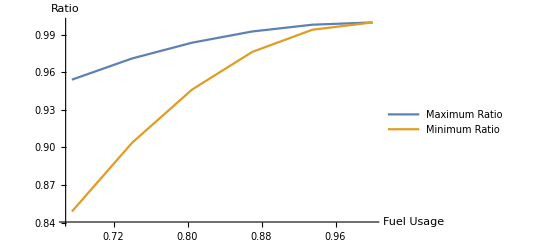

fuelmaxrats.png

```mathematica
Print[maxratios];
Print[minratios];
Range[0.675, 1, (1 - 0.675) / numfuelsamples] 
l1 = ListLinePlot[{{Range[0.675, 1, (1 - 0.675) / numfuelsamples], maxratios} // Transpose,{Range[0.675, 1, (1 - 0.675) / numfuelsamples], minratios} // Transpose}, AxesLabel-> {"Fuel Usage", "Ratio" } , PlotLegends->LineLegend[{"Maximum Ratio","Minimum Ratio"}]]  
Export["fuelmaxrats.png", l1]
```

```mathematica
stats = Table[computestats[tmax, n, tval, m0, fuelpercent, isp, 60], {tval, 60, 7200, 1000}];
maxratios = stats[[;;, 1]];
minratios = stats[[;;, 2]];
Print[maxratios];
Print[minratios];
(**l2 = ListLinePlot[{{Range[0.675, 1, (1 - 0.675) / numfuelsamples], maxratios} // Transpose,{Range[0.675, 1, (1 - 0.675) / numfuelsamples], minratios} // Transpose}, AxesLabel-> {"Fuel Usage", "Ratio" } , PlotLegends->LineLegend[{"Maximum Ratio","Minimum Ratio"}]]  
Export["fuelmaxrats.png", l2]**)
```

0.675

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

{0.0000582765,3.04756×10^-6,11.329}

{0.00346885,0.000374574}

{-0.99863,-0.052336}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

{-0.0000582765,-3.04756×10^-6,11.329}

{-0.00346885,-0.000374574}

{0.99863,0.052336}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.0000324295,-0.000606826}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000553423,-1.47405}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

0.675

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-13.9234,-8.44501×10^7}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{7.73543×10^-6,4.38468×10^-7,12.5317}

{0.00273605,0.00352962}

{-0.99863,0.052336}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.285107,-437537.}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-7.73543×10^-6,-4.38468×10^-7,12.5317}

{-0.00273605,-0.00352962}

{0.99863,-0.052336}

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-1.27061×10^-6,-0.841747}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-5.28996×10^-6,-1.58492×10^-6,11.5179}

{-0.001086,-0.00342053}

{0.965926,0.258819}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.000998226,2211.95}. Try perturbing the initial point(s).

failed to run

{-0.000998226,0.0000183222,220.155}

{-0.398838,-0.396801}

{-0.987688,0.156434}

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-23.1279,1.15716×10^8}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{9.41438×10^-6,4.38468×10^-7,-0.00942343}

{0.00338804,0.00422116}

{-0.99863,0.052336}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

0.675

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.000335549,1936.35}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{1.53931×10^-6,-4.83576×10^-8,1.95472}

{0.000401454,0.000830941}

{-0.838671,0.544639}

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000327663,244.4}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{8.23935×10^-6,2.74497×10^-7,17.1972}

{0.00125,0.00510313}

{-0.891007,0.45399}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-7.39518×10^-6,43.5396}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-1.53931×10^-6,4.83576×10^-8,1.95472}

{-0.000401454,-0.000830941}

{0.838671,-0.544639}

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.0000345237,246.517}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-7.07643×10^-6,-2.74457×10^-7,16.5261}

{-0.00100835,-0.00443043}

{0.891007,-0.45399}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000198551,-0.0181589}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {5.28091×10^-6,-0.00703083}. Try perturbing the initial point(s).

failed to run

{5.28091×10^-6,2.50551×10^-8,-0.00703083}

{0.00105545,0.00308537}

{-0.891007,0.45399}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

0.675

energy computation executed

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0623453,109125.}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{5.03201×10^-6,2.33508×10^-7,14.5684}

{-0.000554175,0.00345768}

{-0.707107,0.707107}

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-2.32231×10^-7,9.9957}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{2.20356×10^-6,4.0339×10^-7,13.9373}

{-0.00128783,0.00195823}

{-0.777146,0.62932}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.0279153,48858.8}. Try perturbing the initial point(s).

failed to run

energy computation executed

trying to run

failed to run

{-5.03201×10^-6,-2.33508×10^-7,14.5684}

{0.000554175,-0.00345768}

{0.707107,-0.707107}

trying to run

failed to run

energy computation executed

trying to run

failed to run

{-2.20356×10^-6,-4.0339×10^-7,13.9373}

{0.00128783,-0.00195823}

{0.777146,-0.62932}

trying to run

failed to run

trying to run

failed to run

trying to run

failed to run

trying to run